```mathematica
de[list_,element_]:=Delete[list,Position[list,element]]
de[{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,17,0,0,20,0,0,23,0,0,26},0]
```

{5,17,20,23,26}

```mathematica
pm[c_,n_]:=Permute[IdentityMatrix[n],c]
```

```mathematica
pm[Cycles[{{1,3}}],3]//MatrixForm
```

(0 | 0 | 1
0 | 1 | 0
1 | 0 | 0)

```mathematica
ta[x_,n_]:=IdentityMatrix[n]+Normal[SparseArray[{{x,x+1},{x+1,x},{x,x},{x+1,x+1}}->{1,1,-1,-1},{n,n}]]
```

```mathematica
d[perm_,n_]:=Table[Piecewise[{{x, Apply[Dot,Map[ta[#,n]&,(1+IntegerDigits[x,n-1])]]==perm}, {0, True}}],{x,1,n^n}]
```

```mathematica
d[({{0, 0, 1}, {0, 1, 0}, {1, 0, 0}}),3]
```

{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,17,0,0,20,0,0,23,0,0,26}

```mathematica
sn[{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,17,0,0,20,0,0,23,0,0,26},3]
```

5

```mathematica
sn[list_,n_]:=First[de[list,0]]
```

```mathematica
ap[n_]:=Table[pm[c,n],{c,SymmetricGroup[n]//GroupElements}]
```

```mathematica
ap[3]
```

```mathematica
Table[First[de[d[i,3],0]],{i,ap[3]}]
```

{3,1,6,10,2,5}

```mathematica
Table[First[de[d[i,4],0]],{i,ap[4]}]
```

First::first: {} has a length of zero and no first element.

{4,2,1,5,7,16,12,6,30,92,19,59,3,11,10,32,34,97,21,48,57,173,102,First[{}]}

```mathematica
Monitor[Table[First[de[Monitor[d[ap[5][[i]],5],x],0]],{i,1,Length[ap[5]]}],i]
```

First::first: {} has a length of zero and no first element.

General::stop: Further output of First :: first will be suppressed during this calculation.

{5,3,2,11,14,46,1,7,6,27,30,110,9,39,25,103,158,414,57,185,121,441,633,1657,20,12,8,35,50,142,68,49,274,1099,198,795,33,135,134,539,542,2158,201,569,793,First[{}],2169,First[{}],4,19,18,75,78,302,17,71,70,283,286,1134,73,295,281,1127,1182,First[{}],313,1209,1145,First[{}],First[{}],First[{}],36,147,100,403,590,1614,132,531,530,2123,2126,First[{}],292,1171,1124,First[{}],First[{}],First[{}],2361,First[{}],First[{}],First[{}],First[{}],First[{}],228,740,484,1764,2532,First[{}],804,2276,First[{}],First[{}],First[{}],First[{}],1252,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}]}

```mathematica
Monitor[Table[First[de[Monitor[d[ap[6][[i]],6],x],0]],{i,1,Length[ap[6]]}],i]
```

First::first: {} has a length of zero and no first element.

General::stop: Further output of First :: first will be suppressed during this calculation.

{6,4,3,19,23,98,2,14,13,69,73,348,17,89,67,339,448,1698,117,492,367,1742,2242,8492,1,9,8,44,48,223,7,39,38,194,198,973,42,214,192,964,1073,4823,242,1117,992,4867,5367,24117,11,59,58,294,298,1473,36,184,183,919,923,4598,292,1464,917,4589,7323,22948,1492,7367,4617,22992,36617,First[{}],86,434,336,1684,2173,8423,211,1059,961,4809,5298,24048,1461,7309,4586,22934,36548,First[{}],10867,42117,26492,First[{}],First[{}],First[{}],586,2461,1836,8711,11211,42461,1211,5586,4961,24336,26836,First[{}],7461,36836,23086,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],30,20,15,79,103,398,10,54,53,269,273,1348,77,389,267,1339,1948,6698,517,1992,1367,6742,9742,33492,130,101,76,384,508,1923,652,507,3263,16319,2538,12694,382,1914,1913,9569,9573,First[{}],2542,9617,12692,First[{}],First[{}],First[{}],51,259,258,1294,1298,6473,257,1289,1288,6444,6448,32223,1292,6464,6442,32214,32323,First[{}],6492,32367,32242,First[{}],First[{}],First[{}],386,1934,1336,6684,9673,33423,1911,9559,9558,First[{}],First[{}],First[{}],6461,32309,32211,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],2586,9961,6836,33711,First[{}],First[{}],12711,First[{}],First[{}],First[{}],First[{}],First[{}],32461,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],5,29,28,144,148,723,27,139,138,694,698,3473,142,714,692,3464,3573,17323,742,3617,3492,17367,17867,First[{}],26,134,133,669,673,3348,132,664,663,3319,3323,16598,667,3339,3317,16589,16698,First[{}],3367,16742,16617,First[{}],First[{}],First[{}],136,684,683,3419,3423,17098,661,3309,3308,16544,16548,First[{}],3417,17089,16542,First[{}],First[{}],First[{}],17117,First[{}],First[{}],First[{}],First[{}],First[{}],711,3559,3461,17309,17798,First[{}],3336,16684,16586,First[{}],First[{}],First[{}],17086,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],3711,18086,17461,First[{}],First[{}],First[{}],16836,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],55,279,278,1394,1398,6973,180,904,903,4519,4523,22598,1392,6964,4517,22589,34823,First[{}],6992,34867,22617,First[{}],First[{}],First[{}],255,1279,1278,6394,6398,31973,1277,6389,6388,31944,31948,First[{}],6392,31964,31942,First[{}],First[{}],First[{}],31992,First[{}],First[{}],First[{}],First[{}],First[{}],680,3404,3403,17019,17023,First[{}],3305,16529,16528,First[{}],First[{}],First[{}],17017,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],6961,34809,22586,First[{}],First[{}],First[{}],31961,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],34961,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],430,2154,1680,8404,10773,42023,1055,5279,4805,24029,26398,First[{}],7305,36529,22930,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],1930,9654,6680,33404,First[{}],First[{}],9555,First[{}],First[{}],First[{}],First[{}],First[{}],32305,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],3555,17779,17305,First[{}],First[{}],First[{}],16680,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],34805,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],2930,12305,9180,43555,First[{}],First[{}],6055,27930,24805,First[{}],First[{}],First[{}],37305,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],12930,First[{}],34180,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],18555,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}]}

```mathematica
Monitor[Table[First[de[Monitor[d[ap[7][[i]],7],x],0]],{i,1,Length[ap[7]]}],i]
TOO LONG
```

```mathematica
SymmetricGroup[4]//GroupElements
```

{Cycles[{}],Cycles[{{3,4}}],Cycles[{{2,3}}],Cycles[{{2,3,4}}],Cycles[{{2,4,3}}],Cycles[{{2,4}}],Cycles[{{1,2}}],Cycles[{{1,2},{3,4}}],Cycles[{{1,2,3}}],Cycles[{{1,2,3,4}}],Cycles[{{1,2,4,3}}],Cycles[{{1,2,4}}],Cycles[{{1,3,2}}],Cycles[{{1,3,4,2}}],Cycles[{{1,3}}],Cycles[{{1,3,4}}],Cycles[{{1,3},{2,4}}],Cycles[{{1,3,2,4}}],Cycles[{{1,4,3,2}}],Cycles[{{1,4,2}}],Cycles[{{1,4,3}}],Cycles[{{1,4}}],Cycles[{{1,4,2,3}}],Cycles[{{1,4},{2,3}}]}

```mathematica
SymmetricGroup[4]//GroupMultiplicationTable//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24
2 | 1 | 4 | 3 | 6 | 5 | 8 | 7 | 10 | 9 | 12 | 11 | 14 | 13 | 16 | 15 | 18 | 17 | 20 | 19 | 22 | 21 | 24 | 23
3 | 5 | 1 | 6 | 2 | 4 | 9 | 11 | 7 | 12 | 8 | 10 | 15 | 17 | 13 | 18 | 14 | 16 | 21 | 23 | 19 | 24 | 20 | 22
4 | 6 | 2 | 5 | 1 | 3 | 10 | 12 | 8 | 11 | 7 | 9 | 16 | 18 | 14 | 17 | 13 | 15 | 22 | 24 | 20 | 23 | 19 | 21
5 | 3 | 6 | 1 | 4 | 2 | 11 | 9 | 12 | 7 | 10 | 8 | 17 | 15 | 18 | 13 | 16 | 14 | 23 | 21 | 24 | 19 | 22 | 20
6 | 4 | 5 | 2 | 3 | 1 | 12 | 10 | 11 | 8 | 9 | 7 | 18 | 16 | 17 | 14 | 15 | 13 | 24 | 22 | 23 | 20 | 21 | 19
7 | 8 | 13 | 14 | 19 | 20 | 1 | 2 | 15 | 16 | 21 | 22 | 3 | 4 | 9 | 10 | 23 | 24 | 5 | 6 | 11 | 12 | 17 | 18
8 | 7 | 14 | 13 | 20 | 19 | 2 | 1 | 16 | 15 | 22 | 21 | 4 | 3 | 10 | 9 | 24 | 23 | 6 | 5 | 12 | 11 | 18 | 17
9 | 11 | 15 | 17 | 21 | 23 | 3 | 5 | 13 | 18 | 19 | 24 | 1 | 6 | 7 | 12 | 20 | 22 | 2 | 4 | 8 | 10 | 14 | 16
10 | 12 | 16 | 18 | 22 | 24 | 4 | 6 | 14 | 17 | 20 | 23 | 2 | 5 | 8 | 11 | 19 | 21 | 1 | 3 | 7 | 9 | 13 | 15
11 | 9 | 17 | 15 | 23 | 21 | 5 | 3 | 18 | 13 | 24 | 19 | 6 | 1 | 12 | 7 | 22 | 20 | 4 | 2 | 10 | 8 | 16 | 14
12 | 10 | 18 | 16 | 24 | 22 | 6 | 4 | 17 | 14 | 23 | 20 | 5 | 2 | 11 | 8 | 21 | 19 | 3 | 1 | 9 | 7 | 15 | 13
13 | 19 | 7 | 20 | 8 | 14 | 15 | 21 | 1 | 22 | 2 | 16 | 9 | 23 | 3 | 24 | 4 | 10 | 11 | 17 | 5 | 18 | 6 | 12
14 | 20 | 8 | 19 | 7 | 13 | 16 | 22 | 2 | 21 | 1 | 15 | 10 | 24 | 4 | 23 | 3 | 9 | 12 | 18 | 6 | 17 | 5 | 11
15 | 21 | 9 | 23 | 11 | 17 | 13 | 19 | 3 | 24 | 5 | 18 | 7 | 20 | 1 | 22 | 6 | 12 | 8 | 14 | 2 | 16 | 4 | 10
16 | 22 | 10 | 24 | 12 | 18 | 14 | 20 | 4 | 23 | 6 | 17 | 8 | 19 | 2 | 21 | 5 | 11 | 7 | 13 | 1 | 15 | 3 | 9
17 | 23 | 11 | 21 | 9 | 15 | 18 | 24 | 5 | 19 | 3 | 13 | 12 | 22 | 6 | 20 | 1 | 7 | 10 | 16 | 4 | 14 | 2 | 8
18 | 24 | 12 | 22 | 10 | 16 | 17 | 23 | 6 | 20 | 4 | 14 | 11 | 21 | 5 | 19 | 2 | 8 | 9 | 15 | 3 | 13 | 1 | 7
19 | 13 | 20 | 7 | 14 | 8 | 21 | 15 | 22 | 1 | 16 | 2 | 23 | 9 | 24 | 3 | 10 | 4 | 17 | 11 | 18 | 5 | 12 | 6
20 | 14 | 19 | 8 | 13 | 7 | 22 | 16 | 21 | 2 | 15 | 1 | 24 | 10 | 23 | 4 | 9 | 3 | 18 | 12 | 17 | 6 | 11 | 5
21 | 15 | 23 | 9 | 17 | 11 | 19 | 13 | 24 | 3 | 18 | 5 | 20 | 7 | 22 | 1 | 12 | 6 | 14 | 8 | 16 | 2 | 10 | 4
22 | 16 | 24 | 10 | 18 | 12 | 20 | 14 | 23 | 4 | 17 | 6 | 19 | 8 | 21 | 2 | 11 | 5 | 13 | 7 | 15 | 1 | 9 | 3
23 | 17 | 21 | 11 | 15 | 9 | 24 | 18 | 19 | 5 | 13 | 3 | 22 | 12 | 20 | 6 | 7 | 1 | 16 | 10 | 14 | 4 | 8 | 2
24 | 18 | 22 | 12 | 16 | 10 | 23 | 17 | 20 | 6 | 14 | 4 | 21 | 11 | 19 | 5 | 8 | 2 | 15 | 9 | 13 | 3 | 7 | 1

```mathematica
PermutationSupport[Cycles[{{1,2,3}}]]
```

{1,2,3}

```mathematica
TransQ[per_]:=Piecewise[{{Piecewise[{{1, PermutationMax[per]-PermutationMin[per]==1}, {0, True}}], PermutationLength[per]==2}, {0, True}}]
```

```mathematica
Map[TransQ,SymmetricGroup[4]//GroupElements]
```

{0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
cs[n_]:=Table[Cycles[{{i,i+1}}],{i,1,n-1}]
```

```mathematica
cs[4]
```

```mathematica
m[c1_,c2_]:=PermutationReplace[c1,c2]
```

```mathematica
Map[PermutationOrder,{Cycles[{{1,2}}],Cycles[{{2,3}}],Cycles[{{3,4}}]}]
```

{2,2,2}

```mathematica
Partition[Map[PermutationOrder,Flatten[Table[m[cs[4][[i]],cs[4][[j]]],{i,1,3},{j,1,3}]]],3]//MatrixForm
```

(2 | 2 | 2
2 | 2 | 2
2 | 2 | 2)

```mathematica
DeleteDuplicates[Flatten[({{Cycles[{{1,2}}], Cycles[{{1,3}}], Cycles[{{1,2}}]}, {Cycles[{{1,3}}], Cycles[{{2,3}}], Cycles[{{2,4}}]}, {Cycles[{{3,4}}], Cycles[{{2,4}}], Cycles[{{3,4}}]}})]]
```

```mathematica
cc={Cycles[{{1,2}}],Cycles[{{1,3}}],Cycles[{{2,3}}],Cycles[{{2,4}}],Cycles[{{3,4}}]};
```

```mathematica
Table[m[cc[[i]],cc[[j]]],{i,1,5},{j,1,5}]//MatrixForm
```

(Cycles[{{1,2}}] | Cycles[{{2,3}}] | Cycles[{{1,3}}] | Cycles[{{1,4}}] | Cycles[{{1,2}}]
Cycles[{{2,3}}] | Cycles[{{1,3}}] | Cycles[{{1,2}}] | Cycles[{{1,3}}] | Cycles[{{1,4}}]
Cycles[{{1,3}}] | Cycles[{{1,2}}] | Cycles[{{2,3}}] | Cycles[{{3,4}}] | Cycles[{{2,4}}]
Cycles[{{1,4}}] | Cycles[{{2,4}}] | Cycles[{{3,4}}] | Cycles[{{2,4}}] | Cycles[{{2,3}}]
Cycles[{{3,4}}] | Cycles[{{1,4}}] | Cycles[{{2,4}}] | Cycles[{{2,3}}] | Cycles[{{3,4}}])

```mathematica
Partition[Map[PermutationOrder,Flatten[Table[m[cc[[i]],cc[[j]]],{i,1,5},{j,1,5}]]],5]//MatrixForm
```

(2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2)

```mathematica
Map[PermutationOrder,SymmetricGroup[4]//GroupElements]
```

{1,2,2,3,3,2,2,2,3,4,4,3,3,4,2,3,2,4,4,3,3,2,4,2}

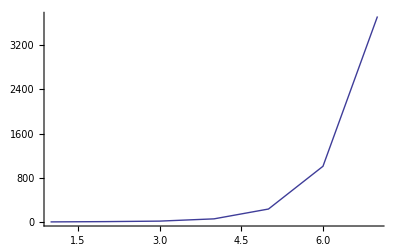

```mathematica
ListPlot[Map[Last,Tally[Map[PermutationMax[#]-PermutationMin[#]&,SymmetricGroup[7]//GroupElements]]],Joined->True]
```

```mathematica
ta[x_,n_]:=IdentityMatrix[n]+Normal[SparseArray[{{x,x+1},{x+1,x},{x,x},{x+1,x+1}}->{1,1,-1,-1},{n,n}]]
d[perm_,n_]:=Table[Piecewise[{{x, Apply[Dot,Map[ta[#,n]&,(1+IntegerDigits[x,n-1])]]==perm}, {0, True}}],{x,1,n^n}]
```

```mathematica
cs[n_]:=Table[Cycles[{{i,i+1}}],{i,1,n-1}]

m[c1_,c2_]:=PermutationReplace[c1,c2]
```

```mathematica
pm[c_,n_]:=Permute[IdentityMatrix[n],c]
```

```mathematica
dd[perm_,n_]:=Piecewise[{{Table[Piecewise[{{x, Apply[Dot,Map[ta[#,n]&,(1+IntegerDigits[x,n-1])]]==pm[perm,n]}, {0, True}}],{x,1,(n-1)^(PermutationOrder[perm])-1}], PermutationMax[perm]-PermutationMin[perm]>1}, {perm, True}}]
```

```mathematica
dd[Cycles[{{1,4,2,3}}],4]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}